```mathematica
Column[Table[Table[Mod[m,n],{n,1,m}],{m,1,17}]]
```

{0}
{0,0}
{0,1,0}
{0,0,1,0}
{0,1,2,1,0}
{0,0,0,2,1,0}
{0,1,1,3,2,1,0}
{0,0,2,0,3,2,1,0}
{0,1,0,1,4,3,2,1,0}
{0,0,1,2,0,4,3,2,1,0}
{0,1,2,3,1,5,4,3,2,1,0}
{0,0,0,0,2,0,5,4,3,2,1,0}
{0,1,1,1,3,1,6,5,4,3,2,1,0}
{0,0,2,2,4,2,0,6,5,4,3,2,1,0}
{0,1,0,3,0,3,1,7,6,5,4,3,2,1,0}
{0,0,1,0,1,4,2,0,7,6,5,4,3,2,1,0}
{0,1,2,1,2,5,3,1,8,7,6,5,4,3,2,1,0}

```mathematica
Grid[Column[Table[Table[Mod[m,n],{n,1,m}],{m,1,17}],Center]]
```

Grid[{0}
{0,0}
{0,1,0}
{0,0,1,0}
{0,1,2,1,0}
{0,0,0,2,1,0}
{0,1,1,3,2,1,0}
{0,0,2,0,3,2,1,0}
{0,1,0,1,4,3,2,1,0}
{0,0,1,2,0,4,3,2,1,0}
{0,1,2,3,1,5,4,3,2,1,0}
{0,0,0,0,2,0,5,4,3,2,1,0}
{0,1,1,1,3,1,6,5,4,3,2,1,0}
{0,0,2,2,4,2,0,6,5,4,3,2,1,0}
{0,1,0,3,0,3,1,7,6,5,4,3,2,1,0}
{0,0,1,0,1,4,2,0,7,6,5,4,3,2,1,0}
{0,1,2,1,2,5,3,1,8,7,6,5,4,3,2,1,0}]

```mathematica
f[x_]:=If[TrueQ[x>b],1,0]
```

```mathematica
d[m_,n_]:=If[TrueQ [Mod[m,n]>0],1,0]
```

```mathematica
t[x_]:=If[x==1,0,1]
```

```mathematica
Column[Table[Table[t[d[m,n]],{n,1,m}],{m,1,17}]]
```

{1}
{1,1}
{1,0,1}
{1,1,0,1}
{1,0,0,0,1}
{1,1,1,0,0,1}
{1,0,0,0,0,0,1}
{1,1,0,1,0,0,0,1}
{1,0,1,0,0,0,0,0,1}
{1,1,0,0,1,0,0,0,0,1}
{1,0,0,0,0,0,0,0,0,0,1}
{1,1,1,1,0,1,0,0,0,0,0,1}
{1,0,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,1,0,0,0,0,0,0,1}
{1,0,1,0,1,0,0,0,0,0,0,0,0,0,1}
{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Column[Table[Table[t[d[m,n]],{n,1,17}],{m,1,17}]]
Manipulate[AdjacencyGraph[Table[Table[d[m,n],{n,1,a}],{m,1,a}]],{a,1,20,1}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}
{1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}
{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}
{1,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}
{1,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}
{1,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0}
{1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0}
{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Manipulate[AdjacencyGraph[Table[Table[t[d[m,n]],{n,1,a}],{m,1,a}]],{a,1,20,1}]
```

```mathematica
Column[Table[Table[d[m,n],{n,1,m}],{m,1,17}],Center]
```

{0}
{0,0}
{0,1,0}
{0,0,1,0}
{0,1,1,1,0}
{0,0,0,1,1,0}
{0,1,1,1,1,1,0}
{0,0,1,0,1,1,1,0}
{0,1,0,1,1,1,1,1,0}
{0,0,1,1,0,1,1,1,1,0}
{0,1,1,1,1,1,1,1,1,1,0}
{0,0,0,0,1,0,1,1,1,1,1,0}
{0,1,1,1,1,1,1,1,1,1,1,1,0}
{0,0,1,1,1,1,0,1,1,1,1,1,1,0}
{0,1,0,1,0,1,1,1,1,1,1,1,1,1,0}
{0,0,1,0,1,1,1,0,1,1,1,1,1,1,1,0}
{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

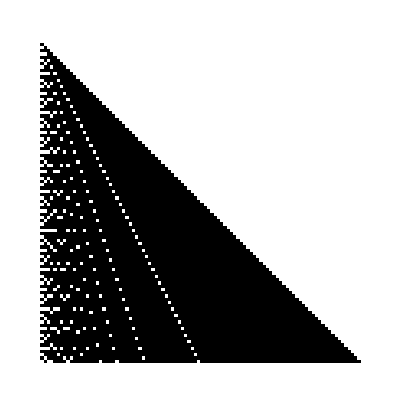

```mathematica
ArrayPlot[Table[Table[d[m,n],{n,1,m}],{m,1,100}],AspectRatio->Automatic]
```

```mathematica
Grid[Table[Table[d[m,n],{n,1,m}],{m,1,20}] ]
```

0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  | 
0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  | 
0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  | 
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  | 
0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 |  | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 
0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0

```mathematica
ArrayPlot[Table[Table[Mod[m,n],{n,1,m}],{m,1,1000}],AspectRatio->Automatic]
```

-Graphics-

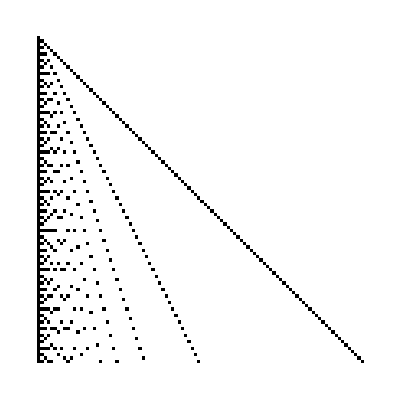

```mathematica
ArrayPlot[Table[Table[t[d[m,n]],{n,1,m}],{m,1,100}],AspectRatio->Automatic]
```

```mathematica
(Table[Mod[n^(Prime[p]-1),Prime[p]],{n,1,x},{p,1,x}]/.x->100)//ArrayPlot
```

Table::iterb: Iterator {n, 1, x} does not have appropriate bounds.

-Graphics-